## Pregunta 1

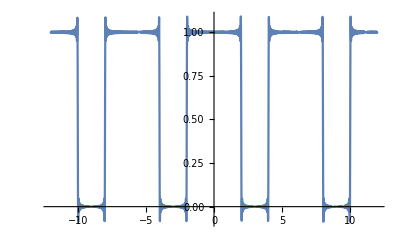

```mathematica
Plot[2/3+2/Pi Sum[1/n Sin[(2 n Pi)/3]Cos[(n Pi t)/3],{n,1,100}],{t,-12,12}]
```

```mathematica
(2/3)^2+1/2 Sum[(2/(n Pi)Sin[2 n Pi/3])^2,{n,1,3}]
```

4/9+15/(8 π^2)

```mathematica
N[4/9+15/(8 π^2)]
```

0.634422

## Pregunta 2

```mathematica
FourierTransform[1/2(DiracDelta[t-(a+b)]+DiracDelta[t-(a-b)]),t,w,FourierParameters->{1,-1}]
```

1/2 (ⅇ^(ⅈ (-a+b) w)+Cos[(a+b) w]-ⅈ Sin[(a+b) w])

## Pregunta 4

```mathematica
k4 = 100;
```

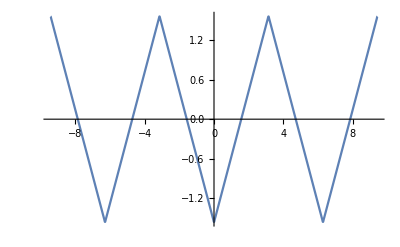

```mathematica
Plot[1/Pi Sum[((-1)^n-1)/n^2 Exp[I n t],{n,-k4,-1}]+1/Pi Sum[((-1)^n-1)/n^2 Exp[I n t],{n,1,k4}],{t,-3Pi,3Pi}]
```

```mathematica
Sum[1/(2n-1)^2,{n,1,Infinity}]
```

π^2/8

```mathematica
Sum[1/(2n-1)^4,{n,1,Infinity}]
```

π^4/96